```mathematica
Clear["Global`*"]
```

```mathematica
phase=Import["Data.xlsx",Path->NotebookDirectory[]][[4]];
phase=Delete[phase,{{1},{2},{3},{4}}];
phase=Delete[phase,Position[phase,""]];
phase=SortBy[phase,First];
```

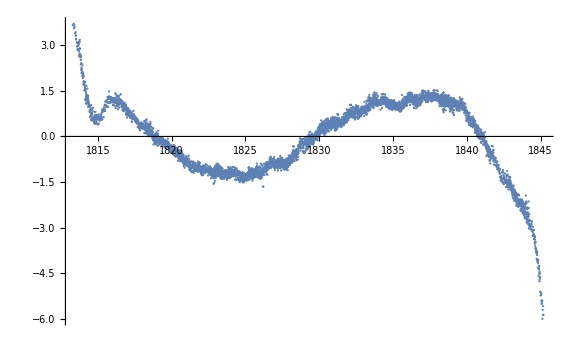

```mathematica
ListPlot[phase,PlotRange->All,ImageSize->Large]
```

```mathematica
test=GatherBy[phase,First];
Table[Mean[test[[i]]],{i,Length[test]}]
```

{{1813.3,3.65648},{1813.36,3.7064},4592,{1845.17,-5.5771},{1845.2,-5.86108}}
 |  |  |  |

```mathematica
specfunc=DeleteDuplicatesBy[phase,First];
```

```mathematica
specfunc[[1;;20]]//MatrixForm
```

(1813.3 | 3.65648
1813.36 | 3.7064
1813.4 | 3.55936
1813.4 | 3.6694
1813.41 | 3.57074
1813.42 | 3.59586
1813.46 | 3.39647
1813.5 | 3.42784
1813.51 | 3.31231
1813.52 | 3.19604
1813.53 | 3.1972
1813.57 | 3.09223
1813.61 | 2.96629
1813.62 | 2.95857
1813.63 | 2.84982
1813.64 | 3.06775
1813.64 | 2.86574
1813.67 | 3.10243
1813.68 | 2.97068
1813.71 | 3.0426)

```mathematica
x={phase[[1,1]]};
i=2;
n=1;
f={phase[[1,2]]};
```

```mathematica
(*Значение функции, отвечающее определенному аргументу, получается усреднением по всем точкам с этим аргументом*)
```

```mathematica
While[i≤Length[phase[[All,1]]],
{
If[phase[[i,1]]==x[[-1]],
{
f[[-1]]=f[[-1]]+phase[[i,2]];
n++; 
},
{
f[[-1]]=f[[-1]]/n;
x=Insert[x,phase[[i,1]],-1];
f=Insert[f,phase[[i,2]],-1];
n=1;
}
];
i++;
}
]
```

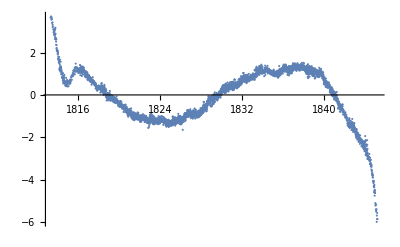

```mathematica
ListPlot[Transpose[{x,f}]]
```

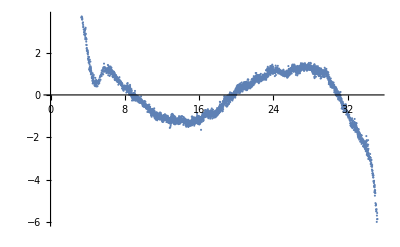

```mathematica
(*Для того, чтобы проще учесть особенность на левом конце, сдвигаем аргумент к нулю*)
phaseRes=f;
xRes=x-1810*Table[1,{i,Dimensions[x][[1]]}];
ListPlot[Transpose[{xRes,phaseRes}]]
```

```mathematica
(*Выполним аппроксимацию данных*)
```

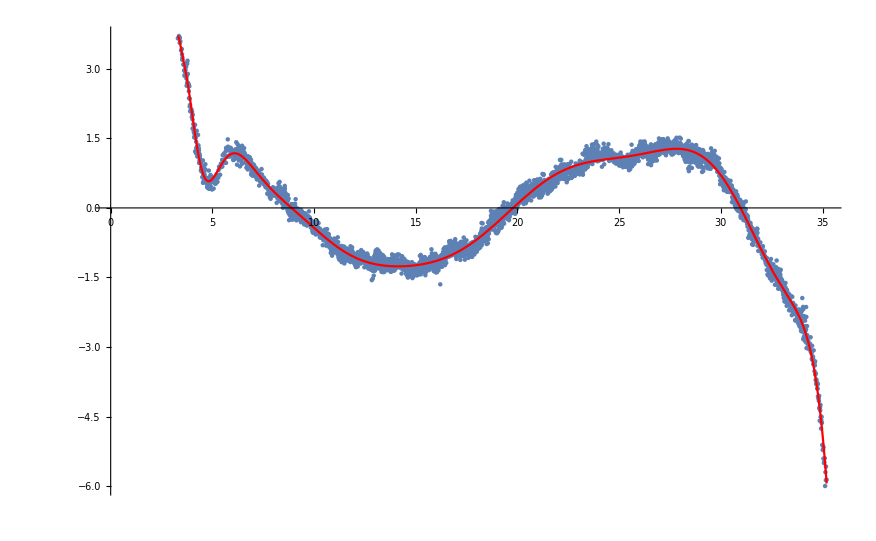

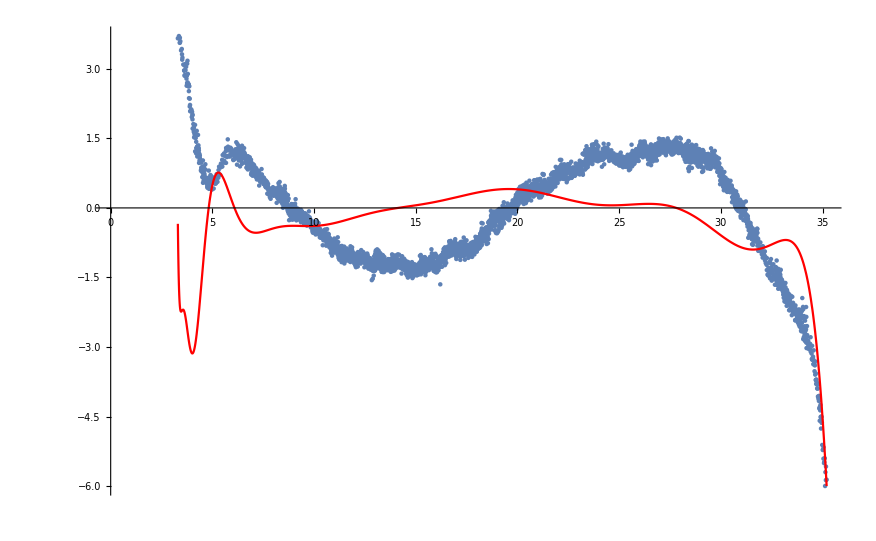

```mathematica
(*В качестве аппроксимирующей функции возьмем кусок ряда Лорана с действительными коэффициентами*)
nfr=10;
nfl=-7;
fitmodel=Sum[Subscript[a,i]*q^i,{i,nfl,nfr}];
fit=FindFit[Transpose[{xRes,phaseRes}],fitmodel,Table[Subscript[a,i],{i,nfl,nfr}],q];Show[ListPlot[Transpose[{xRes,phaseRes}]],Plot[fitmodel/.fit,{q,Min[xRes],Max[xRes]},PlotStyle->Red]]
df=D[fitmodel,q]/.fit;Show[ListPlot[Transpose[{xRes,phaseRes}]],Plot[df,{q,Min[xRes],Max[xRes]},PlotRange->All,PlotStyle->Red]]
```

```mathematica
(*В качестве аппроксимирующей функции возьмем кусок ряда Фурье с действительными коэффициентами*)
```

```mathematica
nF=18;
ω=2*π/(Max[xRes]-Min[xRes]);
fitmodelF=Subscript[a,0]/2+Sum[Subscript[b,i]*Sin[i*ω*q],{i,1,nF}]+Sum[Subscript[a,i]*Cos[i*ω*q],{i,1,nF}];
fit=FindFit[Transpose[{xRes,phaseRes}],fitmodelF,Join[Table[Subscript[a,i],{i,0,nF}],Table[Subscript[b,i],{i,1,nF}]],q];
```

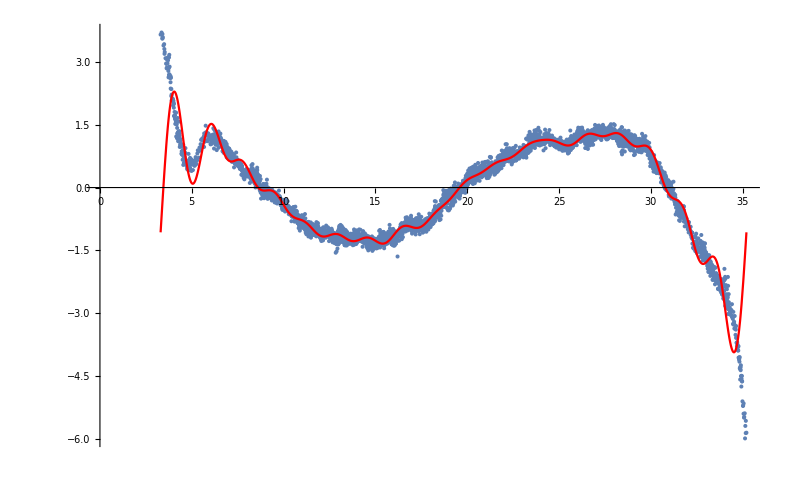

```mathematica
Show[ListPlot[Transpose[{xRes,phaseRes}]],Plot[fitmodelF/.fit,{q,Min[xRes],Max[xRes]},PlotStyle->Red]]
```